# E4: Capacitors and the RC Circuit

Calvin Zikakis
TA: Drew Morrill
Section 311
March 16 2017

## Introduction

In this lab, we explored how different variables can change the properties of a capacitor. A capacitor can be thought as a device capable of storing energy in a circuit, almost all modern electronics use capacitors in some way incorporated into their PCB designs. Throughout this lab we explored the capacitance of parallel plate capacitors by measuring how capacitance changes in relation to plate separation distance. Using this data along with the plate separation and area of the parallel capacitor, we computed the permittivity constant, or the measure of an object’s ability to resist an electric field.  In order to minimize any error, we also measured the stray capacitance which comes from anytime charge is separated. In the second part of the lab we used an oscilloscope to observe the exponential decay of voltage on our parallel plate capacitor. The oscilloscope allowed us to measure the time constant of the RC circuit we were working with. This lab helped us understand the basic workings of a capacitor and how they can be used in everyday circuits in order to make our lives easier.

## Part 1: Capacitance of Parallel Plates

Distance^-1 in m^-1 | Capacitance in F
620.732 | 5.2439×10^-9
310.366 | 2.7339×10^-9
206.911 | 1.8739×10^-9
155.183 | 1.4539×10^-9
124.146 | 1.1939×10^-9
103.455 | 1.0239×10^-9

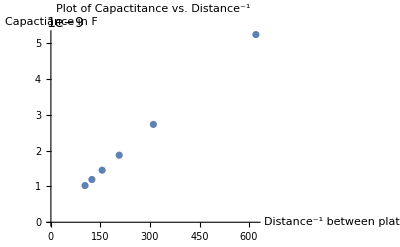

```mathematica
Aplate = 0.93025; (*Plate Area in m^2*)
Cstray= 16.1*10^-12;(*Stray Capacitance in F*)
T = 0.001611; (*Average Thicness of a Nylon Washer in m*)

W = {1,2,3,4,5,6}; (*Number of Washers*)
C1 = {0.526,0.275,0.189,0.147,0.121,0.104}*10^-8; (*Inter-Plate Capacitance in F*)

d = T*W; (*Calculating the actual distance between plate in m*)
C2 = C1-Cstray; (*Calculating the actual Capacitance in F*)

Cvsinvd = Thread[{1/d,C2}]; (*Making the data*)

Grid[Prepend[Cvsinvd,{"Distance^-1 in m^-1","Capacitance in F"}], Frame->All](*Cute Table*)

ListPlot[Cvsinvd, PlotLabel->"Plot of Capactitance vs. Distance^-1",AxesLabel->{"Distance^-1 between plates in m^-1","Capactiance in F"}]
```

My graph shows how capacitance is linearly proportional to distance. The graph shows a very good example of a linear function, which is what is expected.

```mathematica
eps0=(C2*d)/Aplate;
eps0avg =( ∑_(i=1)^Length[eps0] eps0[[i]])/Length[eps0]
eps0sd = √((∑_(i=1)^Length[eps0] (eps0[[i]]-eps0avg)^2)/(Length[eps0]-1));
eps0sdom = eps0sd/√Length[eps0]
```

9.88908×10^-12

2.34493×10^-13

My calculations resulted in a value of ϵ_0 = (9.89 ± 0.23)*10^-12 F/m. The known value of ϵ_0 is ϵ_0 =  8.85 *10^-12 F/m. ϵ_0 has no error because it is defined by μ and c which are both known exact values. In order to calculate whether my answers agree or not, we first need to find the discrepancy. 9.89*10^-12 F/m - 8.85 *10^-12 F/m results in a discrepancy of 1.04 *10^-12 F/m. The error in my measurements is 0.23 *10^-12 F/m which when multiplied by 3 =  0.69 *10^-12 F/m. Because 1.04 *10^-12 F/m >  0.69 *10^-12 F/m, I will have to state that my answer does not agree. There is a couple different reasons this could happen, one being that the stray capacitance reading could have been off. Another possibility for the answers not relating could be from measurement error of the capacitance meter.

## Part 2: Measurement of the Time Constant of an RC Circuit

```mathematica
time = {0, 2.0, 4.0, 6.0, 8.0, 10.0, 12.0, 14.0, 18.0, 22.0, 24.0, 28.0, 32.0}*10^-3; (*Decay Time in s*)
voltage = {3.6, 2.44, 1.76, 1.32, 0.96, .76, .56, .4, .2, .12, .04, 0.001, 0.0001}; (*Decay Voltages in V*)
lnvoltage = Log[voltage]; 
lnvvst = Thread[{time,lnvoltage}]
vvst = Thread[{time, voltage}]
x=time;
y=lnvoltage;
L=Length[x];
```

{{0,1.28093},{0.002,0.891998},{0.004,0.565314},{0.006,0.277632},{0.008,-0.040822},{0.01,-0.274437},{0.012,-0.579818},{0.014,-0.916291},{0.018,-1.60944},{0.022,-2.12026},{0.024,-3.21888},{0.028,-6.90776},{0.032,-9.21034}}

{{0,3.6},{0.002,2.44},{0.004,1.76},{0.006,1.32},{0.008,0.96},{0.01,0.76},{0.012,0.56},{0.014,0.4},{0.018,0.2},{0.022,0.12},{0.024,0.04},{0.028,0.001},{0.032,0.0001}}

According to linfit.nb

-169.08

1.32235

0.206031

0.1087

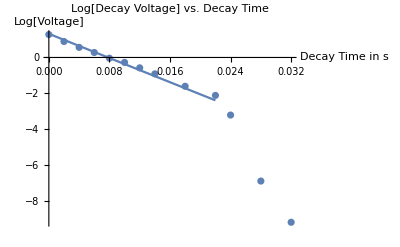

```mathematica
m = -169.08
b = 1.32235
δb  = 0.206031
δm = 0.1087

DataPlot=ListPlot[lnvvst];
TheoryPlot = Plot[m*q+b,{q,0,0.022}];
Show[DataPlot, TheoryPlot,PlotLabel->"Log[Decay Voltage] vs. Decay Time",AxesLabel->{"Decay Time in s","Log[Voltage]"}]
DataPlot2=ListPlot[vvst];
Show[DataPlot2,PlotLabel->"Decay Voltage vs. Decay Time",AxesLabel->{"Decay Time in s","Voltage"}]
```

This plot shows how decaying voltage is linear when graphed on a log scale. This is to be expected. The original data (V(t)) will show as a logarithmic plot, but taking the log of the voltage will scale the graph to a linear function. My larger data points are uniformly scattered around the line of best fit.

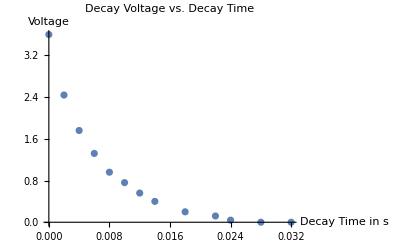

This graph demonstrates voltage as a function of time without a logarithmic scale. This scale shows how voltage exponentially decreases as a function of time. This graph closely matches the shape of the curve visible on the oscilloscope.

```mathematica
tau = -1/m
δtau = Abs[δm/m^2]
```

0.00591436

3.80229×10^-6

Using my data, I calculated the time constant as (5.9144 ± 0.0038)*10^-3 s. The measured time constant I found was (8.16 ± 0.03) * 10^-3s. The discrepancy between these values is (5.9144 ± 0.0038)*10^-3 s -  (8.16 ± 4.41) * 10^-3s =  2.2456 * 10^-3s. The error between the values is calculated as ± 4.445 * 10^-3s. Multiplying that by 3 = 13.36 * 10^-3s. Because 13.36 * 10^-3s >  2.2456 * 10^-3s, we can conclude that my answer agrees.

## Conclusion

In conclusion, this lab introduced us to capacitance and how it is related to distance, area, and time. Part 1 showed us that capacitance and distance are linearly related by showing that as distance increases, so does capacitance. Although my calculated ϵ_0  of (9.89 ± 0.23)*10^-12 did not agree with the measured value, it showed how different errors can propagate easily into the answer resulting in a different value. I believe the source of error from this measurement are from the stray capacitance reading, which could have been off. Another possibility for the answers not relating could be from measurement error of the capacitance meter which would also result in a false measurement which would then propagate into the final calculated ϵ_0. Part 2 of the lab showed us how decaying voltage of a capacitor and time are logarithmically related. This logarithmic relationship helped to teach us a method of fitting a best fit line to logarithmic data by simply taking the log of the voltage. The oscilloscope allowed us to measure and read the relationship of voltage and time. Using the data from this part of the experiment, we were able to successfully measure the time constant. The error we propagated for the time constant resulted in 3.80229×10^-6 which is very low. This low error allowed us to successfully match our measured time constant with our calculated constant proving that our answers matched. “Capacitors and the RC Circuit” helped us gain insight on how capacitors work and the properties assigned with them.